```mathematica
SetDirectory["G:\\毕个业\\basic\\pack"];
FileList=FileNames["*","G:\\毕个业\\basic\\pack\\"];
DisNum=Range[Dimensions[FileList][[1]]];

For[fileNum=1,fileNum<=Dimensions[FileList][[1]],fileNum++,
lengthRatio=Import[StringJoin[FileList[[fileNum]],"\\lengthRatio.csv"]];
v12=Import[StringJoin[FileList[[fileNum]],"\\v12.csv"]];
MinDis=Import[StringJoin[FileList[[fileNum]],"\\MinDis.csv"]];

DisNum[[fileNum]]=Length[MinDis];
];
```

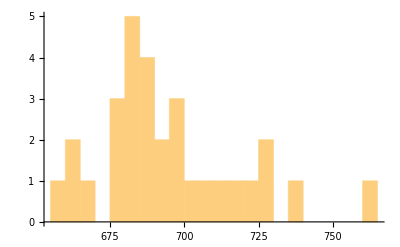

```mathematica
Histogram[DisNum,20]
```